Creates a list res = {r_1,...,r_n}
from the data = {d_1,...,d_n}
as follows:
r_1 = d_1
r_2 = Min(d_1,d_2) = Min(r_1,d_2)
r_3 = Min(d_1,d_2,d_3) = Min(r_2,d_2)
...
r_n = Min(d_1,d_2,d_3,...,d_n) = Min(r_(n-1),d_n)

```mathematica
MinSubLists[data_]:=Module[{value,res},
value=Infinity;
res=Map[(value=Min[value,#])&,data];
res
]
```

Creates a list res = {r_1,...,r_n}
from the list of lists listdata = {l_1,...,l_n} = {{d_(1,1),...,d_(1,m_1)},...,{d_(n,1),...,d_(n,m_n)}}
as follows:
m_min = Min({m_1,...,m_n})
r_1 = {d_(1,1),...,d_(1,m_min)}
...
r_n = {d_(n,1),...,d_(n,m_min)}

```mathematica
MinimumLengthSublists[listdata_]:=Module[{minlength,res},
minlength=Min@Map[Length@#&,listdata];
res=Map[#[[;;minlength]]&,listdata];
res
];
```

{0.328595,0.550824,0.684145,0.766392,0.811146,0.832794,0.84371,0.849875,0.854346,0.858146,0.860806,0.862828,0.864591,0.865803,0.8671,0.868093,0.86897,0.869957,0.870927,0.871841,0.872422,0.872854}

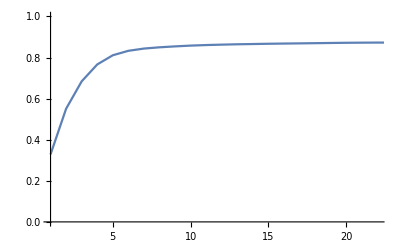

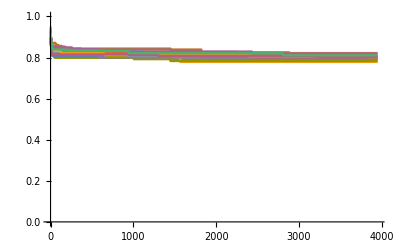

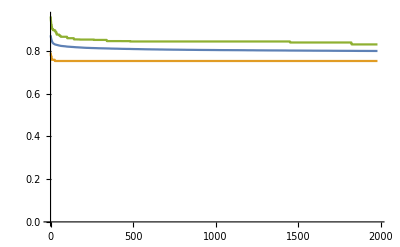

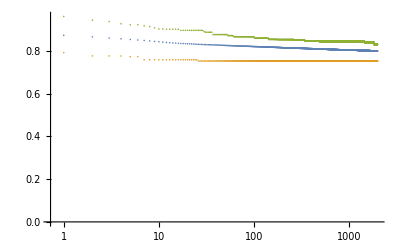

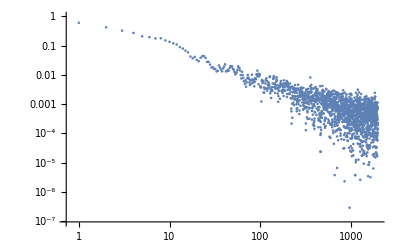

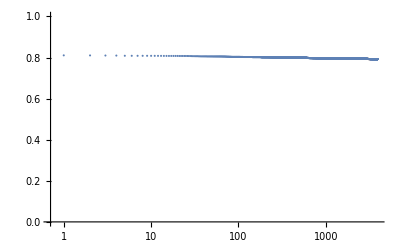

```mathematica
rdata=Map[ToExpression[#]&,Map[StringSplit[#," "]&,ReadList["/run/user/1000/gvfs/sftp:host=lise.jku.austriangrid.at,port=2211,user=k354524/home/k3501/k354524/MasterThesis/Programming/HungarianMethod/cpp/Production/8_0_lammps_2d_pbc_G/results/100_0_0_11.180340_1_0_4000_10/analysis/costmatrix_100_0_0_11.180340_1_0_4000_10.txt",String]]];
rdata=rdata/Max[Flatten@rdata];
ArrayPlot@rdata
n=Length@rdata;
m=22;
Map[Mean[#]&,Table[rdata[[j+i,j]],{i,n-1},{j,1,n-i}]][[;;m]]
ListLinePlot[Map[Mean[#]&,Table[rdata[[j+i,j]],{i,n-1},{j,1,n-i}]],PlotRange->{{1,m},{0,1}}]
ListLinePlot[MinimumLengthSublists@Map[MinSubLists[#[[m;;]]]&,Table[rdata[[i+1;;n,i]],{i,n-1}][[;;30]]],PlotRange->{All,{0,1}}]
tmpdata=MinimumLengthSublists@Map[MinSubLists[#[[m;;]]]&,Table[rdata[[i+1;;n,i]],{i,n-1}][[;;2000]]];
ListLinePlot[{Mean@tmpdata,Map[Min[#]&,tmpdataᵀ],Map[Max[#]&,tmpdataᵀ]},PlotRange->{All,{0,All}}]
ListLogLinearPlot[{Mean@tmpdata,Map[Min[#]&,tmpdataᵀ],Map[Max[#]&,tmpdataᵀ]},PlotRange->{All,{0,All}}]
ListLogLogPlot[
Normalize@Total@Map[-Differences[#]&,MinimumLengthSublists[Map[MinSubLists[#[[m;;]]]&,Table[rdata[[i+1;;n,i]],{i,n-1}][[;;2000]]]]]
,PlotRange->{All,{0,1}}
]
ListLogLinearPlot[Mean@MinimumLengthSublists@Map[MinSubLists[#[[5;;]]]&,Table[rdata[[i+1;;n,i]],{i,n-1}][[;;100]]],PlotRange->{All,{0,1}}]
```

{{0,0},{1,0.328595},{2,0.550824},{3,0.684145},{4,0.766392},{5,0.811146},{6,0.832794},{7,0.84371},3986,{3994,0.917753},{3995,0.920083},{3996,0.907801},{3997,0.897012},{3998,0.8878},{3999,0.885729},{4000,0.881977}}
 |  |  |  |

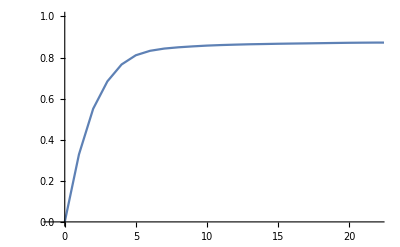

```mathematica
δΓ=Map[Mean[#]&,Table[rdata[[j+i,j]],{i,n-1},{j,1,n-i}]];
δΓfull=Join[{{0,0}},{Range[1,Length@δΓ],δΓ}ᵀ]
ListLinePlot[δΓfull,PlotRange->{{-1,m},{0,1}}]
```

```mathematica
Length@δΓfull
```

4001

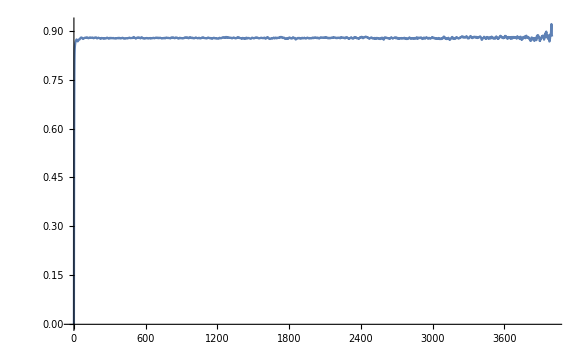

```mathematica
ListLinePlot[δΓfull,PlotRange->All]
```

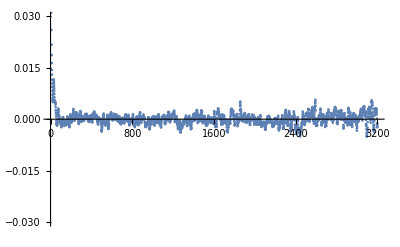

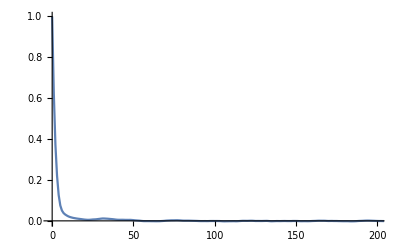

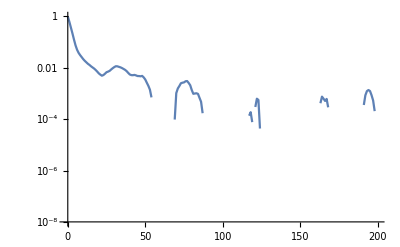

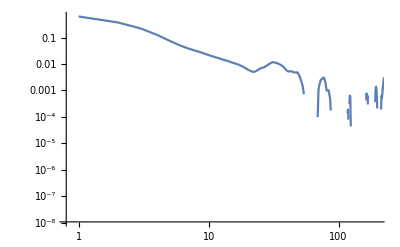

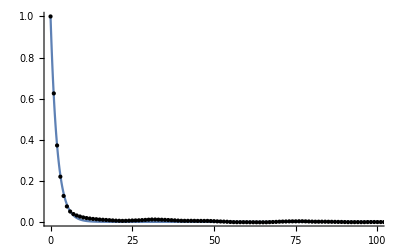

```mathematica
data=δΓfull[[;;Round[Length[δΓfull]*0.8,1]]];
meanmax1=Mean[dataᵀ[[2]][[300;;]]];
data2={dataᵀ[[1]],(1-dataᵀ[[2]]/meanmax1)}ᵀ;
ListPlot[data2,PlotRange->{All,{-0.03,0.03}}]
ListPlot[data2,PlotRange->{{-1,200},All},Joined->True]
ListLogPlot[data2,PlotRange->{{-1,200},All},Joined->True]
ListLogLogPlot[data2,PlotRange->{{-1,200},All},Joined->True]
model=Exp[-k*t];
fit=FindFit[data2,model,{k},t];
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,100},Epilog->Map[Point,data2],PlotRange->All]
```

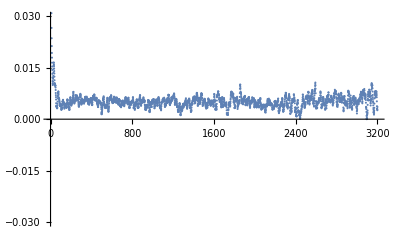

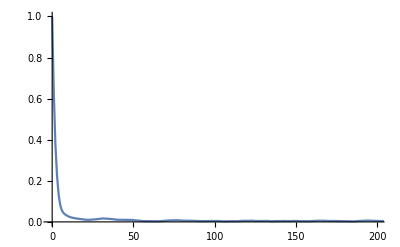

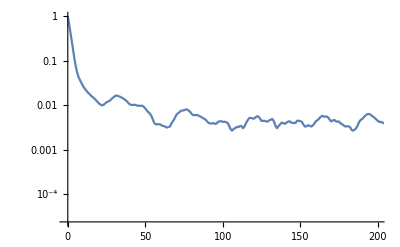

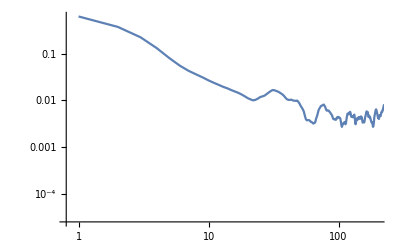

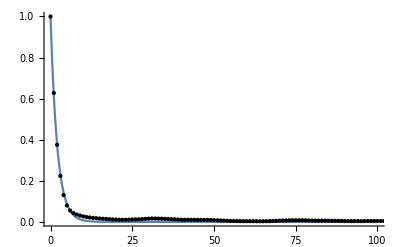

```mathematica
data=δΓfull[[;;Round[Length[δΓfull]*0.8,1]]];
meanmax1=Max[dataᵀ[[2]]];
data2={dataᵀ[[1]],(1-dataᵀ[[2]]/meanmax1)}ᵀ;
ListPlot[data2,PlotRange->{All,{-0.03,0.03}}]
ListPlot[data2,PlotRange->{{-1,200},All},Joined->True]
ListLogPlot[data2,PlotRange->{{-1,200},All},Joined->True]
ListLogLogPlot[data2,PlotRange->{{-1,200},All},Joined->True]
model=Exp[-k*t];
fit=FindFit[data2,model,{k},t];
modelf=Function[{t},Evaluate[model/.fit]];
Plot[modelf[t],{t,0,100},Epilog->Map[Point,data2],PlotRange->All]
```

```mathematica
datasimilarityxy={data1x,(1.0-data1y/Mean[data1y[[300;;Round[n*0.8,1]]]])}ᵀ;
ListPlot[datasimilarityxy,PlotRange->{{-1,100},{-0.03,1}},Joined->False,PlotStyle->Black]
model=Exp[-k*t];
fit=FindFit[datasimilarityxy,model,{k},t]
modelf=Function[{t},Evaluate[model/.fit]];
LogLinearPlot[modelf[t],{t,0,100},Epilog->Map[Point,datasimilarityxy],PlotRange->All]
```

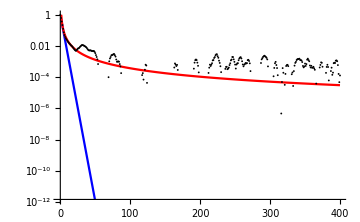
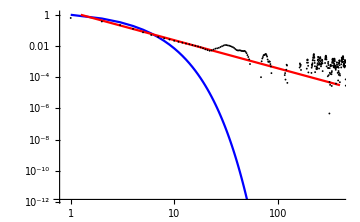
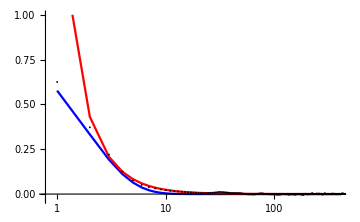

```mathematica
λ1=0.55;
λ2=-1.8;
{ListLogPlot[{datasimilarityxy,Table[Exp[-λ*t],{t,1,400}],1.5*Table[t^λ2,{t,1,400}]},PlotRange->{{-1,400},{-0.03,1}},ImageSize->Medium,Joined->{False,True,True},PlotStyle->{Black,Blue,Red}],
ListLogLogPlot[{datasimilarityxy,Table[Exp[-λ*t],{t,0,400}],1.5*Table[t^λ2,{t,1,400}]},PlotRange->{{-1,400},{-0.03,1}},ImageSize->Medium,Joined->{False,True,True},PlotStyle->{Black,Blue,Red}],
ListLogLinearPlot[{datasimilarityxy,Table[Exp[-λ*t],{t,1,400}],1.5*Table[t^λ2,{t,1,400}]},PlotRange->{{-1,400},{-0.03,1}},ImageSize->Medium,Joined->{False,True,True},PlotStyle->{Black,Blue,Red}]}
```

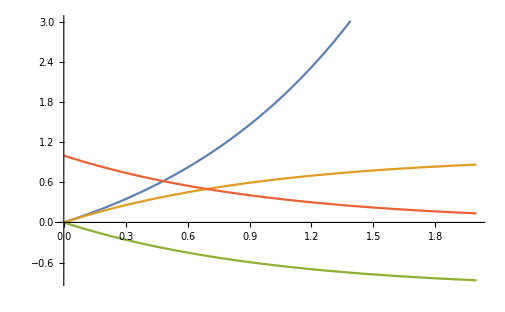

```mathematica
Plot[{Exp[t]-1,1-Exp[-t],Exp[-t]-1,Exp[-t]},{t,0,2}]
```

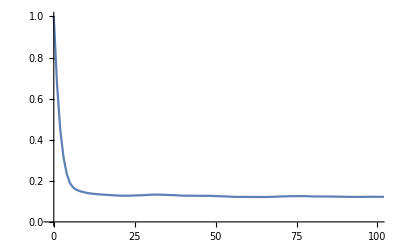

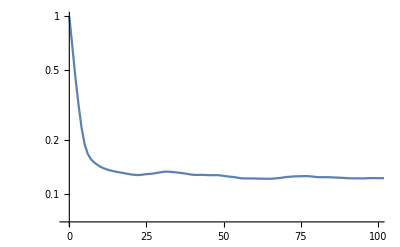

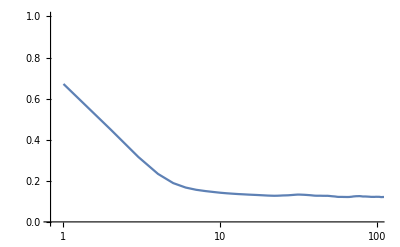

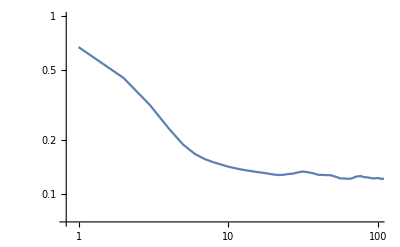

```mathematica
ListPlot[{data1xyᵀ[[1]],1-data1xyᵀ[[2]]}ᵀ,PlotRange->{{-1,100},{0,1}},Joined->True]
ListLogPlot[{data1xyᵀ[[1]],1-data1xyᵀ[[2]]}ᵀ,PlotRange->{{-1,100},{0,1}},Joined->True]
ListLogLinearPlot[{data1xyᵀ[[1]],1-data1xyᵀ[[2]]}ᵀ,PlotRange->{{-1,100},{0,1}},Joined->True]
ListLogLogPlot[{data1xyᵀ[[1]],1-data1xyᵀ[[2]]}ᵀ,PlotRange->{{-1,100},{0,1}},Joined->True]
```